```mathematica
str1="This is a String"
str2="This is a sentence. Sentences are made of words"
str3=StringTake[WikipediaData["computer"],100]
```

This is a String

This is a sentence. Sentences are made of words

A computer is a device that can be instructed to carry out sequences of arithmetic or logical operat

```mathematica
StringTake[str1,6]
StringTake[{"hello","world"},2]
```

This i

{he,wo}

```mathematica
StringLength[str1]
StringReverse[str1]
ToUpperCase[str1]
StringJoin["Hello ","world"]
InputForm[Sort[Characters[str1]]]
```

16

gnirtS a si sihT

THIS IS A STRING

Hello world

{" ", " ", " ", "a", "g", "h", "i", "i", "i", "n", "r", "s", "s", "S", "t", "T"}

```mathematica
TextWords[str2]
TextSentences[str2]
```

{This,is,a,sentence,Sentences,are,made,of,words}

{This is a sentence.,Sentences are made of words}

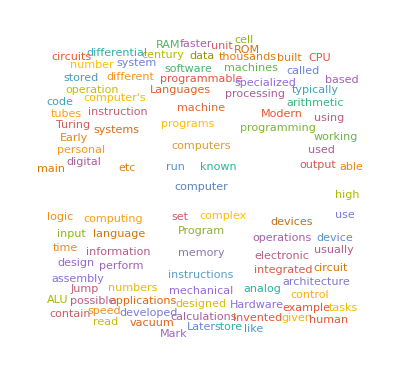

```mathematica
WordCloud[WikipediaData["computer"]]
```

```mathematica
Length[WordList[]]
Take[WordList[],20]
```

40127

{a,aah,aardvark,aback,abacus,abaft,abalone,abandon,abandoned,abandonment,abase,abasement,abash,abashed,abashment,abate,abatement,abattoir,abbe,abbess}

{I,II,III,IV,V,VI,VII,VIII,IX,X,XI,XII,XIII,XIV,XV,XVI,XVII,XVIII,XIX,XX,XXI,XXII,XXIII,XXIV,XXV,XXVI,XXVII,XXVIII,XXIX,XXX,XXXI,XXXII,XXXIII,XXXIV,XXXV,XXXVI,XXXVII,XXXVIII,XXXIX,XL,XLI,XLII,XLIII,XLIV,XLV,XLVI,XLVII,XLVIII,XLIX,L,LI,LII,LIII,LIV,LV,LVI,LVII,LVIII,LIX,LX,LXI,LXII,LXIII,LXIV,LXV,LXVI,LXVII,LXVIII,LXIX,LXX,LXXI,LXXII,LXXIII,LXXIV,LXXV,LXXVI,LXXVII,LXXVIII,LXXIX,LXXX,LXXXI,LXXXII,LXXXIII,LXXXIV,LXXXV,LXXXVI,LXXXVII,LXXXVIII,LXXXIX,XC,XCI,XCII,XCIII,XCIV,XCV,XCVI,XCVII,XCVIII,XCIX,C}

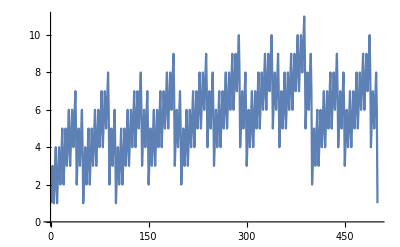

```mathematica
Table[RomanNumeral[x],{x,100}]
ListLinePlot[Table[StringLength[RomanNumeral[x]],{x,500}]]
```

{one,two,three,four,five,six,seven,eight,nine,ten,eleven,twelve,thirteen,fourteen,fifteen,sixteen,seventeen,eighteen,nineteen,twenty,twenty-one,twenty-two,twenty-three,twenty-four,twenty-five,twenty-six,twenty-seven,twenty-eight,twenty-nine,thirty,thirty-one,thirty-two,thirty-three,thirty-four,thirty-five,thirty-six,thirty-seven,thirty-eight,thirty-nine,forty,forty-one,forty-two,forty-three,forty-four,forty-five,forty-six,forty-seven,forty-eight,forty-nine,fifty,fifty-one,fifty-two,fifty-three,fifty-four,fifty-five,fifty-six,fifty-seven,fifty-eight,fifty-nine,sixty,sixty-one,sixty-two,sixty-three,sixty-four,sixty-five,sixty-six,sixty-seven,sixty-eight,sixty-nine,seventy,seventy-one,seventy-two,seventy-three,seventy-four,seventy-five,seventy-six,seventy-seven,seventy-eight,seventy-nine,eighty,eighty-one,eighty-two,eighty-three,eighty-four,eighty-five,eighty-six,eighty-seven,eighty-eight,eighty-nine,ninety,ninety-one,ninety-two,ninety-three,ninety-four,ninety-five,ninety-six,ninety-seven,ninety-eight,ninety-nine,one hundred}

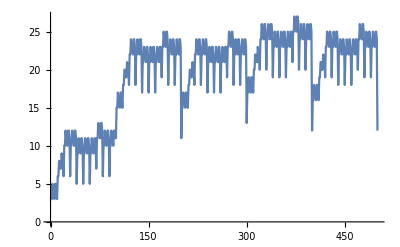

```mathematica
Table[IntegerName[x],{x,100}]
ListLinePlot[Table[StringLength[IntegerName[x]],{x,500}]]
```

```mathematica
Alphabet[]
LetterNumber[Alphabet[]]
FromLetterNumber[Range[26]]
Alphabet["Russian"]
Transliterate[Alphabet["Russian"]]
Transliterate["wolfram","Russian"]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26}

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

{а,б,в,г,д,е,ё,ж,з,и,й,к,л,м,н,о,п,р,с,т,у,ф,х,ц,ч,ш,щ,ъ,ы,ь,э,ю,я}

{a,b,v,g,d,e,e,z,z,i,j,k,l,m,n,o,p,r,s,t,u,f,h,c,c,s,s,",y,',e,u,a}

уолфрам

```mathematica
tmp1=Rasterize[Style["ABC",100]]
EdgeDetect[tmp1]
```

-Graphics-

-Graphics-

```mathematica
RandomWord[10]
```

{spinelessness,tilde,dignity,acrobatic,illegitimate,commutation,suffice,fingerprinting,wantonly,colossus}